## Use Stirling Numbers to Define Chromatic Polynomials

```mathematica
chromaticPolynomial[n_]:=Simplify[FunctionExpand[Sum[StirlingS2[n,i]*FactorialPower[q,i]*(q-i)^n,{i,1,n}]]]
```

```mathematica
chromaticRoots[n_]:=N/@Solve[chromaticPolynomial[n]==0, q]
```

#### Magnitudes of Roots

```mathematica
chromaticRoots[70]
```

{{q→0.},{q→1.},{q→2.},{q→3.},{q→4.},{q→5.},{q→6.},{q→7.},{q→8.},{q→9.},{q→10.},{q→11.},{q→12.},{q→13.},{q→14.},{q→15.},{q→16.},{q→17.},{q→18.},{q→19.},{q→20.},{q→21.},{q→22.},{q→23.},{q→24.},{q→25.},{q→26.},{q→27.},{q→28.},{q→29.},{q→30.},{q→31.},{q→32.0001},{q→32.9307},{q→33.3217-0.558973 ⅈ},{q→33.3217+0.558973 ⅈ},{q→33.6845-1.35784 ⅈ},{q→33.6845+1.35784 ⅈ},{q→34.0432-2.16944 ⅈ},{q→34.0432+2.16944 ⅈ},{q→34.3979-2.99839 ⅈ},{q→34.3979+2.99839 ⅈ},{q→34.7482-3.84513 ⅈ},{q→34.7482+3.84513 ⅈ},{q→35.0943-4.71015 ⅈ},{q→35.0943+4.71015 ⅈ},{q→35.436-5.59394 ⅈ},{q→35.436+5.59394 ⅈ},{q→35.7732-6.49703 ⅈ},{q→35.7732+6.49703 ⅈ},{q→36.1058-7.41993 ⅈ},{q→36.1058+7.41993 ⅈ},{q→36.434-8.36318 ⅈ},{q→36.434+8.36318 ⅈ},{q→36.7575-9.32736 ⅈ},{q→36.7575+9.32736 ⅈ},{q→37.0763-10.3131 ⅈ},{q→37.0763+10.3131 ⅈ},{q→37.3906-11.3209 ⅈ},{q→37.3906+11.3209 ⅈ},{q→37.7002-12.3516 ⅈ},{q→37.7002+12.3516 ⅈ},{q→38.0051-13.4057 ⅈ},{q→38.0051+13.4057 ⅈ},{q→38.3056-14.4841 ⅈ},{q→38.3056+14.4841 ⅈ},{q→38.6014-15.5876 ⅈ},{q→38.6014+15.5876 ⅈ},{q→38.8928-16.717 ⅈ},{q→38.8928+16.717 ⅈ},{q→39.1797-17.8732 ⅈ},{q→39.1797+17.8732 ⅈ},{q→39.4622-19.0571 ⅈ},{q→39.4622+19.0571 ⅈ},{q→39.7405-20.2698 ⅈ},{q→39.7405+20.2698 ⅈ},{q→40.0144-21.5123 ⅈ},{q→40.0144+21.5123 ⅈ},{q→40.2843-22.7858 ⅈ},{q→40.2843+22.7858 ⅈ},{q→40.55-24.0916 ⅈ},{q→40.55+24.0916 ⅈ},{q→40.8117-25.4309 ⅈ},{q→40.8117+25.4309 ⅈ},{q→41.0695-26.8051 ⅈ},{q→41.0695+26.8051 ⅈ},{q→41.3236-28.2158 ⅈ},{q→41.3236+28.2158 ⅈ},{q→41.5739-29.6646 ⅈ},{q→41.5739+29.6646 ⅈ},{q→41.8206-31.1532 ⅈ},{q→41.8206+31.1532 ⅈ},{q→42.0639-32.6836 ⅈ},{q→42.0639+32.6836 ⅈ},{q→42.3039-34.2578 ⅈ},{q→42.3039+34.2578 ⅈ},{q→42.5406-35.8781 ⅈ},{q→42.5406+35.8781 ⅈ},{q→42.7744-37.547 ⅈ},{q→42.7744+37.547 ⅈ},{q→43.0052-39.2673 ⅈ},{q→43.0052+39.2673 ⅈ},{q→43.2333-41.0419 ⅈ},{q→43.2333+41.0419 ⅈ},{q→43.4589-42.8744 ⅈ},{q→43.4589+42.8744 ⅈ},{q→43.6821-44.7685 ⅈ},{q→43.6821+44.7685 ⅈ},{q→43.9032-46.7286 ⅈ},{q→43.9032+46.7286 ⅈ},{q→44.1225-48.7597 ⅈ},{q→44.1225+48.7597 ⅈ},{q→44.3401-50.8675 ⅈ},{q→44.3401+50.8675 ⅈ},{q→44.5564-53.0586 ⅈ},{q→44.5564+53.0586 ⅈ},{q→44.7717-55.341 ⅈ},{q→44.7717+55.341 ⅈ},{q→44.9864-57.7239 ⅈ},{q→44.9864+57.7239 ⅈ},{q→45.2011-60.2189 ⅈ},{q→45.2011+60.2189 ⅈ},{q→45.4162-62.8399 ⅈ},{q→45.4162+62.8399 ⅈ},{q→45.6325-65.6049 ⅈ},{q→45.6325+65.6049 ⅈ},{q→45.8509-68.5371 ⅈ},{q→45.8509+68.5371 ⅈ},{q→46.0726-71.6677 ⅈ},{q→46.0726+71.6677 ⅈ},{q→46.2994-75.0411 ⅈ},{q→46.2994+75.0411 ⅈ},{q→46.5339-78.7238 ⅈ},{q→46.5339+78.7238 ⅈ},{q→46.7805-82.826 ⅈ},{q→46.7805+82.826 ⅈ},{q→47.0478-87.5591 ⅈ},{q→47.0478+87.5591 ⅈ},{q→47.3588-93.471 ⅈ},{q→47.3588+93.471 ⅈ}}

```mathematica
(*try for n=10*)
Abs[q/.chromaticRoots[10]]
```

{0.,1.,2.,3.,4.00037,4.86746,5.25673,5.25673,5.81053,5.81053,6.51764,6.51764,7.43619,7.43619,8.64425,8.64425,10.2702,10.2702,12.6146,12.6146}

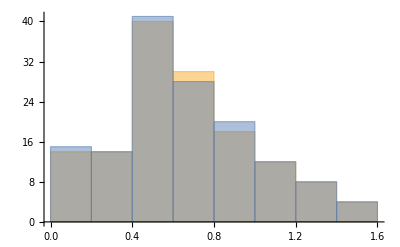

```mathematica
Histogram[Table[Abs[(q/n)/.chromaticRoots[n]],{n,70,71}]]
```

### Fitting Curves to Roots

```mathematica
filterRoots[roots_]:=Module[{newroots=List[]},
			For[i=1,i<=Length[roots], i++,If[Im[roots[[i]]]>0,AppendTo[newroots,roots[[i]]],0]];
Return[newroots]]
```

```mathematica
MapThread[List,{Re[Flatten[Table[filterRoots[(q/n - 4/(Pi*E))/.chromaticRoots[n]],{n,70,71}]]],Im[Flatten[Table[filterRoots[(q/n)/.chromaticRoots[n]],{n,70,71}]]]}]
```

{{0.00762594,0.00798533},{0.0128082,0.0193977},{0.0179333,0.0309921},{0.0229993,0.0428341},{0.0280047,0.0549304},{0.0329484,0.0672878},{0.0378294,0.0799135},{0.0426466,0.0928147},{0.0473991,0.105999},{0.0520864,0.119474},{0.0567078,0.133248},{0.0612631,0.147329},{0.0657521,0.161727},{0.070175,0.176451},{0.074532,0.19151},{0.0788235,0.206916},{0.0830502,0.22268},{0.0872125,0.238814},{0.0913114,0.255331},{0.0953477,0.272244},{0.0993224,0.289568},{0.103236,0.307318},{0.107091,0.325512},{0.110887,0.344165},{0.114626,0.363298},{0.118309,0.38293},{0.121938,0.403083},{0.125514,0.42378},{0.129039,0.445046},{0.132515,0.466908},{0.135943,0.489397},{0.139325,0.512544},{0.142664,0.536386},{0.145961,0.560961},{0.14922,0.586313},{0.152442,0.612491},{0.155631,0.63955},{0.15879,0.667552},{0.161922,0.696567},{0.165031,0.726678},{0.168121,0.75798},{0.171197,0.790585},{0.174265,0.824627},{0.177331,0.86027},{0.180404,0.897713},{0.183494,0.937213},{0.186614,0.979101},{0.189781,1.02382},{0.193021,1.07202},{0.196371,1.12463},{0.199894,1.18323},{0.203713,1.25084},{0.208155,1.3353},{0.00643493,0.00546171},{0.0114482,0.0164696},{0.0165168,0.0278368},{0.0215267,0.0394427},{0.0264781,0.0512938},{0.0313698,0.0633966},{0.036201,0.0757579},{0.0409704,0.0883846},{0.0456774,0.101284},{0.0503212,0.114463},{0.0549012,0.12793},{0.0594171,0.141692},{0.0638686,0.155758},{0.0682559,0.170137},{0.072579,0.184838},{0.0768384,0.199872},{0.0810345,0.215248},{0.0851679,0.230979},{0.0892392,0.247075},{0.0932493,0.26355},{0.097199,0.280417},{0.101089,0.297691},{0.104921,0.315386},{0.108696,0.33352},{0.112414,0.352108},{0.116077,0.37117},{0.119687,0.390726},{0.123244,0.410797},{0.126751,0.431406},{0.130209,0.452577},{0.133619,0.474338},{0.136983,0.496718},{0.140304,0.519749},{0.143583,0.543466},{0.146823,0.567907},{0.150026,0.593117},{0.153194,0.619143},{0.15633,0.64604},{0.159438,0.673868},{0.16252,0.702699},{0.165581,0.732613},{0.168624,0.763703},{0.171655,0.796082},{0.174679,0.829883},{0.177702,0.865265},{0.180733,0.902428},{0.183782,0.941626},{0.186861,0.983186},{0.189989,1.02755},{0.19319,1.07535},{0.1965,1.12751},{0.199983,1.18561},{0.203761,1.25264},{0.208156,1.33633}}

```mathematica
test=FindFit[MapThread[List,{Re[Flatten[Table[filterRoots[(q/n-4/(Pi*E))/.chromaticRoots[n]],{n,100,101}]]],Im[Flatten[Table[filterRoots[(q/n)/.chromaticRoots[n]],{n,100,101}]]]}],a*b^x+c,{a,b,c},x]
```

{a→0.112479,b→196901.,c→-0.0939158}

```mathematica
Log[(b/.test)]/Log[(/.)]
```

```mathematica
A/.test
```

4.42346

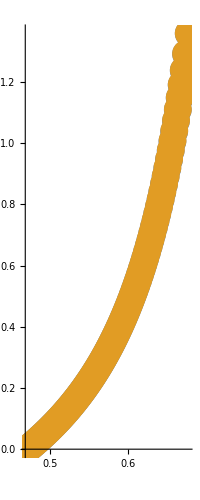

```mathematica
points=ComplexListPlot[Table[Flatten[filterRoots[(q/n)/.chromaticRoots[n]]],{n,100,101}], PlotStyle->PointSize[0.05]]
```

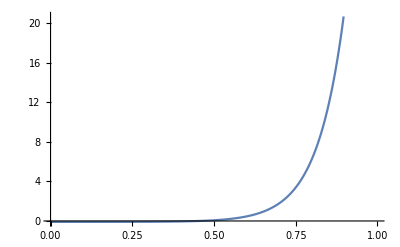

```mathematica
curve=Plot[(a/.test)*(b/.test)^(x-4/(Pi*E))+(c/.test),{x,0,1}]
```

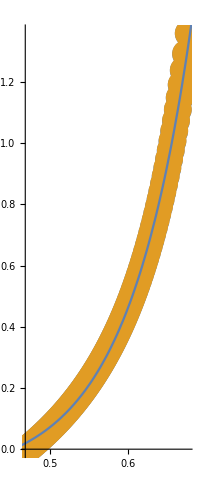

ComplexListPlot::lpn: {{},{{0.75,0.433013}},«8»,«10»} is not a list of numbers or pairs of numbers.

ComplexListPlot[{{},{0.75+0.433013 ⅈ},{0.619787+0.164045 ⅈ,0.713547+0.649561 ⅈ},{0.535774+0.0393191 ⅈ,0.638603+0.340307 ⅈ,0.700622+0.774361 ⅈ},{0.590063+0.196832 ⅈ,0.646877+0.466417 ⅈ,0.693873+0.858237 ⅈ},{0.555994+0.114805 ⅈ,0.60859+0.30877 ⅈ,0.651674+0.560847 ⅈ,0.689742+0.919445 ⅈ},{0.530795+0.0647865 ⅈ,0.579303+0.212891 ⅈ,0.619898+0.39761 ⅈ,0.654825+0.634878 ⅈ,0.686972+0.966538 ⅈ},{0.504844+0.0292997 ⅈ,0.55598+0.148768 ⅈ,0.594505+0.293596 ⅈ,0.627613+0.470455 ⅈ,0.657068+0.694849 ⅈ,0.685001+1.00415 ⅈ},{0.536932+0.103212 ⅈ,0.573567+0.221582 ⅈ,0.605224+0.361873 ⅈ,0.633231+0.531581 ⅈ,0.658759+0.744643 ⅈ,0.683537+1.03503 ⅈ},{0.521111+0.069105 ⅈ,0.555961+0.168909 ⅈ,0.586307+0.284676 ⅈ,0.613212+0.420642 ⅈ,0.637514+0.583787 ⅈ,0.660089+0.786794 ⅈ,0.682414+1.06094 ⅈ},{0.508788+0.0433958 ⅈ,0.540958+0.128842 ⅈ,0.570055+0.227018 ⅈ,0.595989+0.340046 ⅈ,0.619405+0.471909 ⅈ,0.640896+0.629012 ⅈ,0.661169+0.823037 ⅈ,0.68153+1.08306 ⅈ},{0.495593+0.0242671 ⅈ,0.52806+0.0974375 ⅈ,0.555928+0.182383 ⅈ,0.580951+0.278813 ⅈ,0.603609+0.389146 ⅈ,0.624352+0.517122 ⅈ,0.64364+0.668652 ⅈ,0.662069+0.854605 ⅈ,0.680821+1.10222 ⅈ},{0.516905+0.0722859 ⅈ,0.543543+0.146876 ⅈ,0.567685+0.230741 ⅈ,0.589642+0.325351 ⅈ,0.609768+0.433064 ⅈ,0.628401+0.55736 ⅈ,0.645916+0.703743 ⅈ,0.662835+0.8824 ⅈ,0.680243+1.11899 ⅈ},{0.507051+0.0516228 ⅈ,0.532614+0.118013 ⅈ,0.555893+0.192037 ⅈ,0.577178+0.274668 ⅈ,0.596744+0.367456 ⅈ,0.614855+0.472634 ⅈ,0.63178+0.593452 ⅈ,0.647838+0.735071 ⅈ,0.663496+0.9071 ⅈ,0.679764+1.13384 ⅈ},{0.49899+0.0343111 ⅈ,0.52292+0.0941348 ⅈ,0.545347+0.160244 ⅈ,0.565979+0.23345 ⅈ,0.585012+0.314792 ⅈ,0.60266+0.405778 ⅈ,0.619129+0.508513 ⅈ,0.634645+0.626046 ⅈ,0.649486+0.763247 ⅈ,0.664076+0.929227 ⅈ,0.679363+1.14709 ⅈ},{0.490975+0.0211104 ⅈ,0.514286+0.0740748 ⅈ,0.53587+0.133696 ⅈ,0.55586+0.199295 ⅈ,0.574378+0.271585 ⅈ,0.591592+0.351619 ⅈ,0.607667+0.440838 ⅈ,0.622775+0.541225 ⅈ,0.637109+0.655657 ⅈ,0.650917+0.788753 ⅈ,0.66459+0.949187 ⅈ,0.679024+1.159 ⅈ},{0.506592+0.0570257 ⅈ,0.527321+0.111221 ⅈ,0.546678+0.170553 ⅈ,0.564692+0.235511 ⅈ,0.581487+0.306841 ⅈ,0.597198+0.385569 ⅈ,0.611963+0.473063 ⅈ,0.625924+0.571197 ⅈ,0.639252+0.682701 ⅈ,0.652173+0.811974 ⅈ,0.665051+0.967302 ⅈ,0.678735+1.16978 ⅈ},{0.499588+0.0423687 ⅈ,0.519584+0.0919691 ⅈ,0.538314+0.146053 ⅈ,0.555832+0.204951 ⅈ,0.572218+0.269202 ⅈ,0.587583+0.339552 ⅈ,0.602035+0.416987 ⅈ,0.61569+0.502803 ⅈ,0.628673+0.59878 ⅈ,0.641136+0.707518 ⅈ,0.653287+0.833223 ⅈ,0.665466+0.983833 ⅈ,0.678487+1.17959 ⅈ},{0.493501+0.0293649 ⅈ,0.512561+0.0753084 ⅈ,0.530673+0.124938 ⅈ,0.5477+0.178747 ⅈ,0.563686+0.23713 ⅈ,0.578712+0.30064 ⅈ,0.59287+0.370004 ⅈ,0.606252+0.446163 ⅈ,0.618956+0.530352 ⅈ,0.631095+0.624265 ⅈ,0.642806+0.730389 ⅈ,0.654281+0.852756 ⅈ,0.665844+0.998992 ⅈ,0.678272+1.18857 ⅈ},{0.488041+0.0189819 ⅈ,0.506164+0.0607534 ⅈ,0.523673+0.106565 ⅈ,0.540216+0.156042 ⅈ,0.555807+0.209484 ⅈ,0.570502+0.267306 ⅈ,0.584374+0.330055 ⅈ,0.597501+0.398436 ⅈ,0.609962+0.473345 ⅈ,0.621844+0.555959 ⅈ,0.633247+0.647898 ⅈ,0.644298+0.751548 ⅈ,0.655177+0.870786 ⅈ,0.66619+1.01295 ⅈ,0.678085+1.19682 ⅈ}}]

```mathematica
Show[points,curve]
```

```mathematica
chromaticRoots[10]
```

### Real Plot of Polynomials

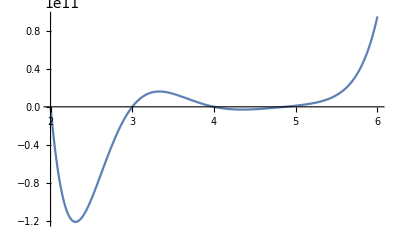

```mathematica
Plot[chromaticPolynomial[10],{q,2,6}]
```

```mathematica
Plot[chromaticPolynomial[20],{q,-0.1,11}]
```

-Graphics-

### Complex Plot of Polynomials

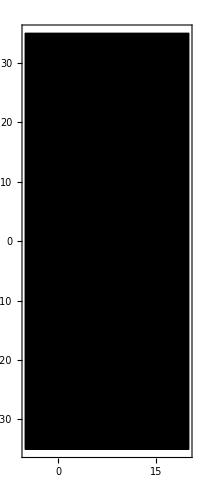

```mathematica
ComplexPlot[chromaticPolynomial[20],{q,-5-35I,20+35I},ColorFunction->"CyclicLogAbsArg",PlotLegends->Automatic]
```

```mathematica
fit=FindFit[MapThread[List,{Table[n,{n,2,20}],Table[chromaticPolynomial[n]/.q->5,{n,2,20}]}], a*b^x,{a,b,c},x]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a→226.166,b→5.31235,c→1.}

```mathematica
pointsEval=ListPlot[MapThread[List,{Table[n,{n,2,20}],Table[chromaticPolynomial[n]/.q->5,{n,2,20}]}]]
```

-Graphics-

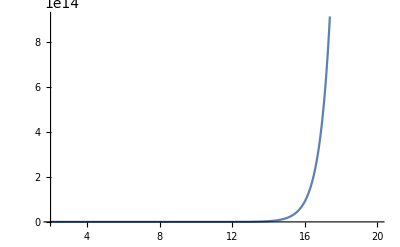

```mathematica
curveEval=Plot[(a/.fit)*(b/.fit)^x+(c/.fit),{x,2,20}]
```

```mathematica
Show[{pointsEval,curveEval}]
```

-Graphics-

```mathematica
ListPlot[Table[StirlingS2[40,i],{i,0,40}]]
```

-Graphics-

```mathematica
N[StirlingS2[40,14]/StirlingS2[40,15]]
```

1.25404

```mathematica
Flatten[Table[Position[Table[StirlingS2[n,i],{i,0,n}],Max[Table[StirlingS2[n,i],{i,0,n}]]],{n,0,60}]]
```

{1,2,2,3,3,3,4,4,5,5,5,6,6,6,7,7,7,8,8,8,9,9,9,10,10,10,11,11,11,11,12,12,12,13,13,13,13,14,14,14,15,15,15,15,16,16,16,16,17,17,17,17,18,18,18,18,19,19,19,19,20,20}

```mathematica
N[StirlingS2[60,19]/StirlingS2[60,20]]
```

1.1379

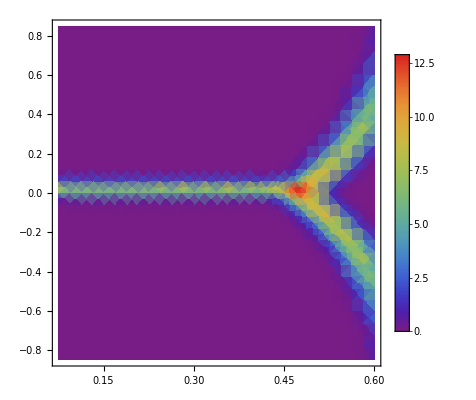

```mathematica
SmoothDensityHistogram[MapThread[List,{Re[Flatten[Table[(q/n)/.chromaticRoots[n],{n,50,52}]]],Im[Flatten[Table[(q/n)/.chromaticRoots[n],{n,50,52}]]]}],0.02,"PDF",ColorFunction->"Rainbow",Mesh->0,PlotLegends->Automatic]
```